```mathematica
Dens[en_]=FourierTransform[(BesselJ[0,t/2])^2/Sqrt[2Pi],t,en,Assumptions->en>-1&&en<1]
```

(2 EllipticK[1-en^2])/π^2

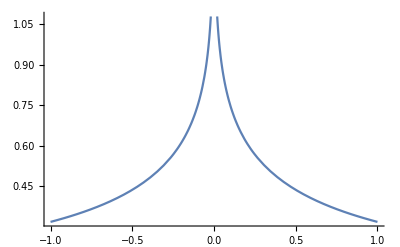

```mathematica
Plot[Dens[x],{x,-1,1}]
```

```mathematica
Denstab={N@#,N@Dens[#]}&/@Table[i/10000,{i,-10000,10000}]
```

{{-1.,0.31831},{-0.9999,0.318326},{-0.9998,0.318342},{-0.9997,0.318358},{-0.9996,0.318374},{-0.9995,0.318389},{-0.9994,0.318405},{-0.9993,0.318421},{-0.9992,0.318437},{-0.9991,0.318453},19981,{0.9991,0.318453},{0.9992,0.318437},{0.9993,0.318421},{0.9994,0.318405},{0.9995,0.318389},{0.9996,0.318374},{0.9997,0.318358},{0.9998,0.318342},{0.9999,0.318326},{1.,0.31831}}
 |  |  |  |

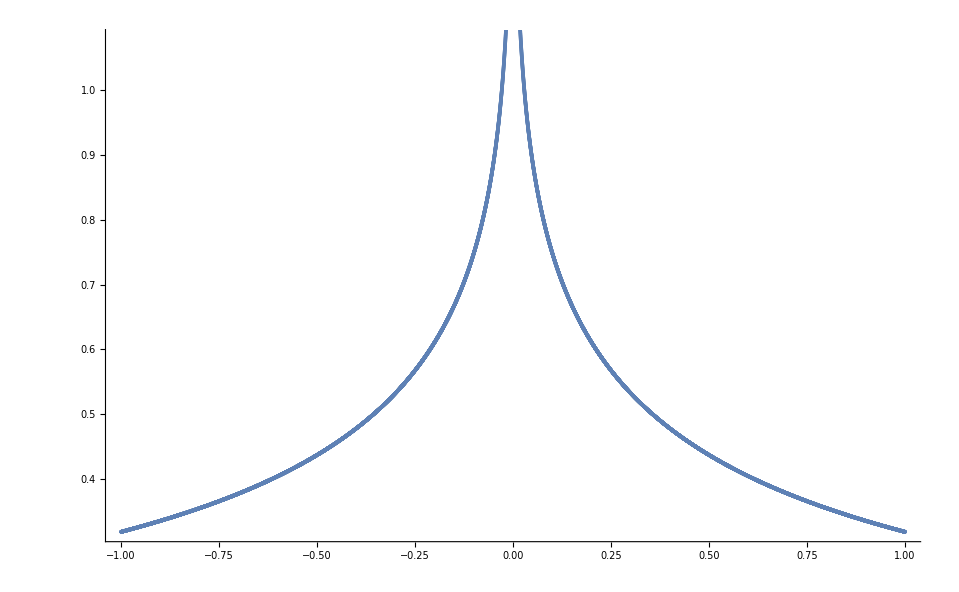

```mathematica
Show[{Plot[Dens[x],{x,-1,1}],ListPlot[Denstab]}]
```

```mathematica
Export["dens2d.dat",Denstab]
```

dens2d.dat

```mathematica
ekin[beta_]:=NIntegrate[2.0*Dens[x]*x/(Exp[x*beta]+1),{x,-1,1}]
```

```mathematica
betatab={13.0,14.0,15.6,17.4,19.6,22.4,26.1,32.4,39.4,52.8,65.0,80.0}
```

{13.,14.,15.6,17.4,19.6,22.4,26.1,32.4,39.4,52.8,65.,80.}

```mathematica
ekintab={#,ekin[#]}&/@Table[100000.0/i,{i,1,10000}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

{{100000.,-0.405285},{50000.,-0.405285},{33333.3,-0.405285},{25000.,-0.405285},{20000.,-0.405285},{16666.7,-0.405285},{14285.7,-0.405285},{12500.,-0.405285},9984,{10.007,-0.384188},{10.006,-0.384185},{10.005,-0.384181},{10.004,-0.384178},{10.003,-0.384174},{10.002,-0.38417},{10.001,-0.384167},{10.,-0.384163}}
 |  |  |  |

```mathematica
Export["EkinU0.dat",ekintab]
```

EkinU0.dat

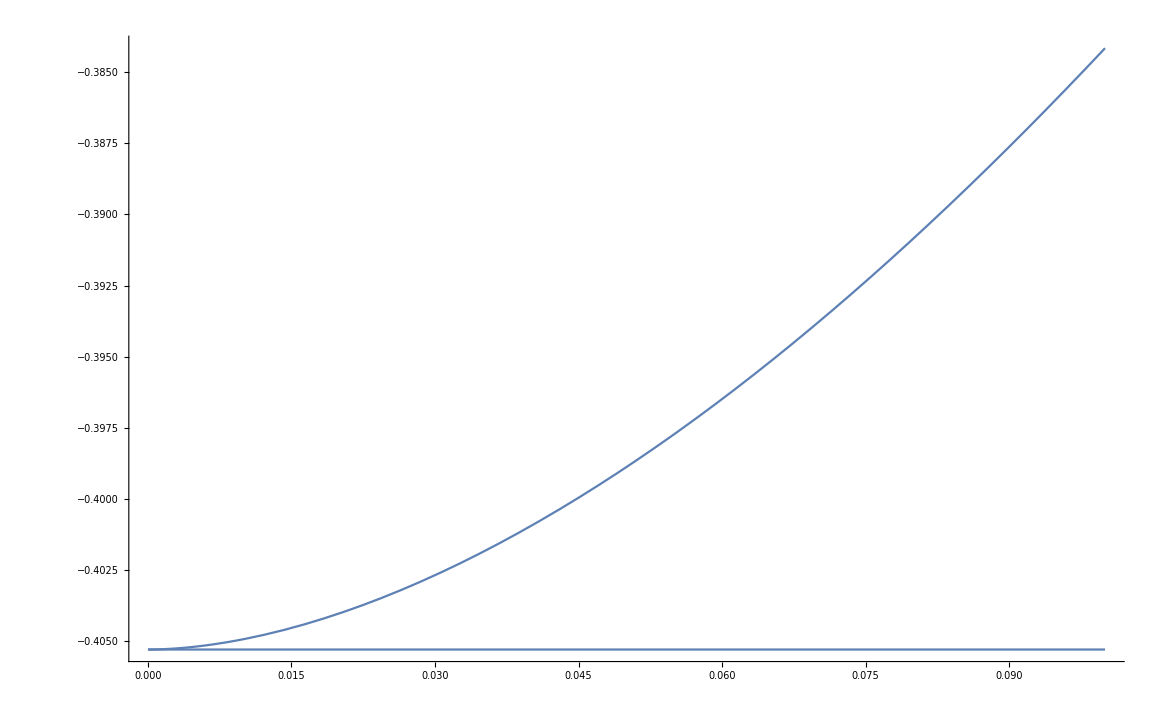

```mathematica
Show[Plot[ekin[1/x],{x,0.00001,0.1}],ListPlot[ekintab,Joined->True],Plot[-4/Pi^2,{x,0.00001,0.1}]]
```

```mathematica
Integrate[2*Dens[x]*x,{x,-1,0}]
```

-4/π^2

```mathematica
(*Calculate E_kin and E_pot with the DMFT self-energy*)
(*Calculation only for half-filling!!! Out of half-filling-> replace eps-> eps-m+Un/2*)
fermi[beta_,eps_]:=1/(Exp[beta*eps]+1)
```

```mathematica
zero1[U_,eps_]:=(1/2)*(eps+Sqrt[eps^2+U^2])
```

```mathematica
zero2[U_,eps_]:=(1/2)*(eps-Sqrt[eps^2+U^2])
```

```mathematica
ekinAL[U_,beta_]:=(4/Pi^2)*NIntegrate[Sqrt[eps^2+U^2]^(-1)*(fermi[beta,zero1[U,eps]]*(eps+U^2/(4*zero1[U,eps]))-fermi[beta,zero2[U,eps]]*(eps+U^2/(4*zero2[U,eps])))*EllipticK[1-eps^2]*eps,{eps,-1,1}]
```

```mathematica
epotAL[U_,beta_]:=(U/4)*(1+(2*U/Pi^2)*NIntegrate[Sqrt[eps^2+U^2]^(-1)*(fermi[beta,zero1[U,eps]]-fermi[beta,zero2[U,eps]])*EllipticK[1-eps^2],{eps,-1,1}])
```

```mathematica
ekinALtab={#,ekinAL[4,#]}&/@Table[100000.0/i,{i,1,10000}]
```

{{100000.,-0.0614358},{50000.,-0.0614358},{33333.3,-0.0614358},{25000.,-0.0614358},{20000.,-0.0614358},{16666.7,-0.0614358},{14285.7,-0.0614358},{12500.,-0.0614358},9985,{10.006,-0.0614358},{10.005,-0.0614358},{10.004,-0.0614358},{10.003,-0.0614358},{10.002,-0.0614358},{10.001,-0.0614358},{10.,-0.0614358}}
 |  |  |  |

```mathematica
Export["EkinAL_U4.dat",ekinALtab]
```

EkinAL_U4.dat

```mathematica
epotALtab={#,epotAL[4,#]}&/@Table[100000.0/i,{i,1,10000}]
```

{{100000.,0.00761868},{50000.,0.00761868},{33333.3,0.00761868},{25000.,0.00761868},{20000.,0.00761868},{16666.7,0.00761868},{14285.7,0.00761868},{12500.,0.00761868},9985,{10.006,0.00761871},{10.005,0.00761871},{10.004,0.00761871},{10.003,0.00761871},{10.002,0.00761871},{10.001,0.00761871},{10.,0.00761871}}
 |  |  |  |

```mathematica
Export["EpotAL_U4.dat",epotALtab]
```

EpotAL_U4.dat